```mathematica
qiblas=With[
{q=  {{, Qibla, City, Country}, {RGBColor[1, 0, 0], "Petra", "Wadi Musa", "Jordan"}, {RGBColor[0, 1, 0], "Kaāba", "Mecca", "SaudiArabia"}, {RGBColor[0, 0, 1], "al-Aqsa", "Jerusalem", "Israel"}}   },

If[ListQ[q],q,Rest/@Rest@First@q]];
```

```mathematica
compareQibla[city_, orientation_: 0]:=Module[{q,
c={Red,Green,Blue,Gray},p=Point@{0,0},
direction=GeoDirection@@Map[#~CityData~"Coordinates"&,{##}]&,
a=Arrow@AnglePath[{π/2-#}]&},
q=Riffle[c,First/@qiblas];
c=Riffle[c,a[city~direction~Rest@#]&/@qiblas];
If[orientation!=0,p=a[orientation];q~AppendTo~"Mosque Orientation"];
p=Graphics[{Thick,Sequence@@c,p,Dashed,Dashing@Small,Circle[]},
ImageSize->Medium,PlotLabel->city~StringRiffle~", "];
Row@{p, LineLegend@@Thread@Partition[q,2]}]
```

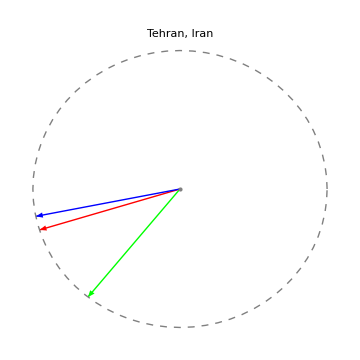

```mathematica
compareQibla[{"Tehran","Iran"}]
```

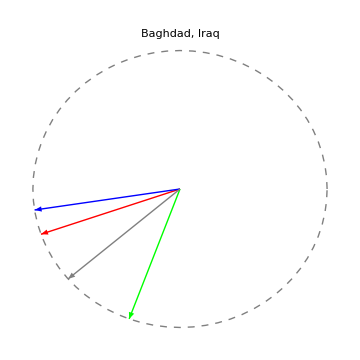

```mathematica
compareQibla[{"Baghdad","Iraq"},229.5°]
```

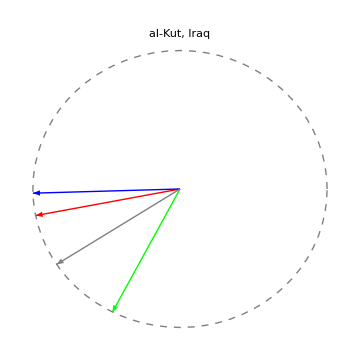

```mathematica
compareQibla[{"al-Kut","Iraq"},237°]
```

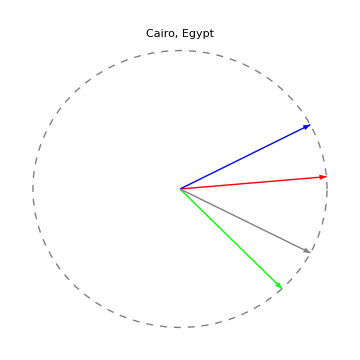

```mathematica
compareQibla[{"Cairo","Egypt"},117.5°]
```

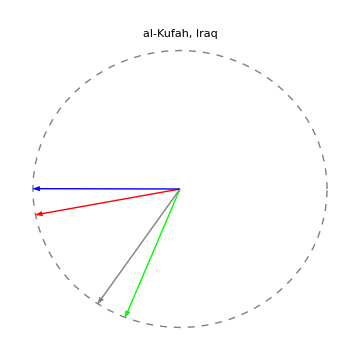

```mathematica
compareQibla[{"al-Kufah","Iraq"},214°]
```